# NG^23 T_04. Метод k-средних и RBF-сети

КМ2021, курс 2, семестр 4
доц. Малевич А.Э.
23-фев-2023

## Задание 1

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Dimensions[Data = Import["NG23T04Problem.xlsx",{"Sheets","Ковалевская Варвара"}]]
```

{3000,3}

```mathematica
BBox=Map[MinMax,Data[[All,{1,2}]]ᵀ]
```

{{-14.6843,291.946},{49.2336,342.681}}

```mathematica
Map[Dimensions, {Train,Test}=Partition[Data,UpTo@Round[0.8 Length@Data]]]
Map[Dimensions, {Train,TrainLabel}={Train[[All,;;2]],Rationalize@Train[[All,-1]]}]
Map[Dimensions, {Test,TestLabel}={Test[[All,;;2]],Rationalize@Test[[All,-1]]}]
```

{{2400,3},{600,3}}

{{2400,2},{2400}}

{{600,2},{600}}

```mathematica
Length[indBlue = Flatten@Position[TrainLabel,+1]]
Length[indRed = Flatten@Position[TrainLabel,-1]]
%%+%
```

969

1431

2400

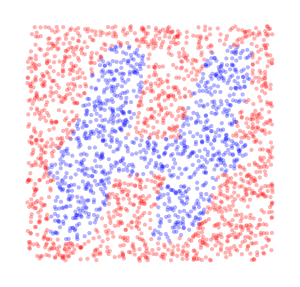

```mathematica
Fig1=Graphics[{PointSize@Small,Opacity@0.3,Blue, Point@Train[[indBlue]],Red,Point@Train[[indRed]]},AspectRatio->Automatic,ImageSize->300]
```

## Задание 2

```mathematica
cBlue=Train[[RandomSample[indBlue,20]]];
cRed=Train[[RandomSample[indRed,20]]];
```

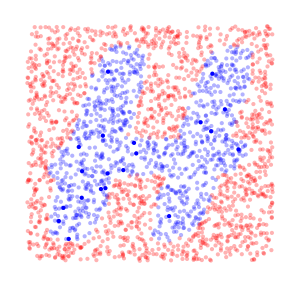

```mathematica
Show[Fig1,Graphics[{PointSize@Medium,Blue,Point@cBlue}]]
```

```mathematica
Step = 0;
CreatePalette@Show[Fig1,Graphics[{PointSize@Medium,Blue,Point@Dynamic@cBlue,Red,Point@Dynamic@cRed}],WindowTitle->ToString@StringForm["Шаг: ",Dynamic@Step]];
```

```mathematica
Nearest[cBlue->"Index",Train[[indBlue[[32]]]]]
```

{15}

```mathematica
Sow[#,First@Nearest[cBlue->"Index",Train[[#]]]]&/@indBlue;
```

```mathematica
Map[Dimensions,Last@Reap[Sow[#,First@Nearest[cBlue->"Index",Train[[#]]]]&/@indBlue]]
```

{{34},{60},{43},{94},{121},{17},{121},{44},{89},{34},{61},{47},{21},{48},{15},{17},{49},{26},{19},{9}}

```mathematica
cBlue=Map[Mean@Train[[#]]&,clusterBlue=Last@Reap[Sow[#,First@Nearest[cBlue->"Index",Train[[#]]]]&/@indBlue]]
```

{{117.151,208.442},{235.242,178.481},{54.2745,122.363},{230.924,286.905},{100.099,280.69},{73.508,135.108},{176.805,115.754},{41.8067,161.59},{81.1706,220.773},{46.5161,196.662},{208.067,191.227},{236.412,245.122},{108.564,166.625},{188.396,213.951},{45.4318,85.0823},{23.5191,95.7497},{147.576,177.612},{33.0132,120.666},{81.2154,166.312},{82.9649,138.257}}

```mathematica
clusterBlue[[3]]
```

{5,6,40,123,131,270,271,333,376,389,463,530,656,670,701,710,770,844,857,902,973,996,1030,1031,1071,1113,1114,1130,1178,1403,1443,1471,1564,1565,1661,1699,1785,1826,1844,1883,2153,2166,2226}

```mathematica
Do[Step++;If[PossibleZeroQ@Max@Abs[cBlue-#],Break[],cBlue=#]&@Map[Mean@Train[[#]]&,clusterBlue=Last@Reap[Sow[#,First@Nearest[cBlue->"Index",Train[[#]]]]&/@indBlue]]
,{100}]
Do[Step++;If[PossibleZeroQ@Max@Abs[cRed-#],Break[],cRed=#]&@Map[Mean@Train[[#]]&,clusterRed=Last@Reap[Sow[#,First@Nearest[cRed->"Index",Train[[#]]]]&/@indRed]]
,{100}]
```

## Задание 3

```mathematica
statBlue=Through@{Mean,Covariance}@Train[[#]]&/@clusterBlue;
statRed=Through@{Mean,Covariance}@Train[[#]]&/@clusterRed;
```

{{101.637,229.658},{{85.9765,22.4621},{22.4621,124.615}}}

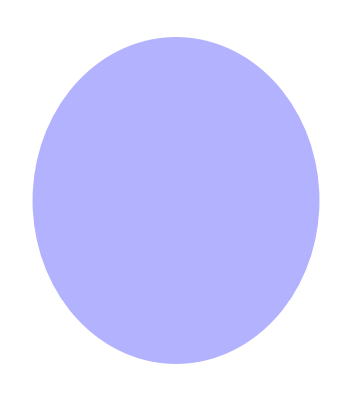

```mathematica
statBlue[[13]]
Graphics[{Opacity@0.3,Blue,{Ellipsoid@@%}}]
```

{{101.637,229.658},{{85.9765,22.4621},{22.4621,124.615}}}

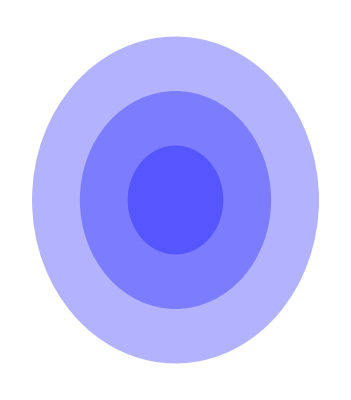

```mathematica
statBlue[[13]]
Graphics[{Opacity@0.3,Blue,{Ellipsoid[#1,#2],Ellipsoid[#1,4 #2],Ellipsoid[#1,9 #2]}&@@%}]
```

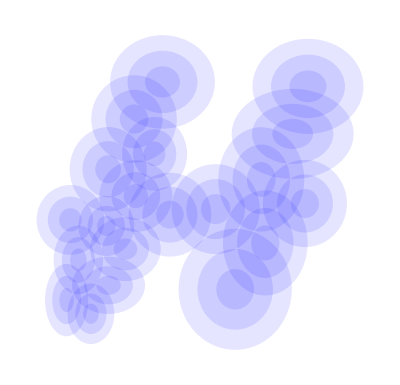

```mathematica
Graphics[{Opacity@0.1,Blue,{Ellipsoid[#1,#2],Ellipsoid[#1,4 #2],Ellipsoid[#1,9 #2]}&@@@statBlue}]
```

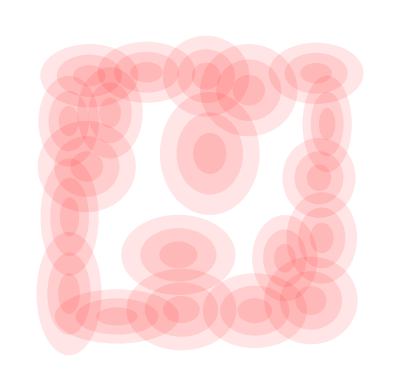

```mathematica
Graphics[{Opacity@0.1,Red,{Ellipsoid[#1,#2],Ellipsoid[#1,4 #2],Ellipsoid[#1,9 #2]}&@@@statRed}]
```

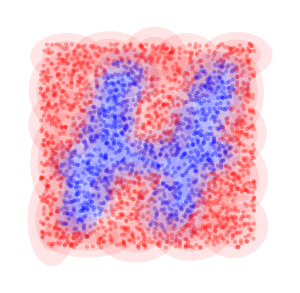

```mathematica
Show[Fig1,Graphics[{Opacity@0.1,Blue,{Ellipsoid[#1,#2],Ellipsoid[#1,4 #2],Ellipsoid[#1,9 #2]}&@@@statBlue}],Graphics[{Opacity@0.1,Red,{Ellipsoid[#1,#2],Ellipsoid[#1,4 #2],Ellipsoid[#1,9 #2]}&@@@statRed}]]
```

## Задание 4

```mathematica
3;
statBlue[[5]]
With[{sC =-0.5  (%%)^-2 Inverse[Last@%], μ=First@%},Exp[sC.(#-μ).(#-μ)]&]
%@{3,2}
```

{{108.632,293.423},{{228.347,-49.1401},{-49.1401,201.273}}}

Exp[{{-0.000256787,-0.0000626935},{-0.0000626935,-0.000291327}}.(#1-{108.632,293.423}).(#1-{108.632,293.423})]&

2.15834×10^-14

```mathematica
ClearAll[kmRBF];
kmRBF[{μ_,C_},s_:3]:=With[{sC =-0.5  s^-2 Inverse[C]},Exp[sC.(#-μ).(#-μ)]&]
```

```mathematica
BBox//MatrixForm
Sequence@@ArrayFlatten@({{{{x},{y}},BBox}})
```

(-14.6843 | 291.946
49.2336 | 342.681)

Sequence[{x,-14.6843,291.946},{y,49.2336,342.681}]

```mathematica
kmRBF[statRed[[19]]]
With[{xy=Sequence@@ArrayFlatten@({{{{x},{y}},BBox}})},
Plot3D[%@{x,y},xy,PlotRange->All,ColorFunction->"GreenPinkTones"]]
```

Exp[{{-0.000234814,0.0000194949},{0.0000194949,-0.000264429}}.(#1-{148.771,323.541}).(#1-{148.771,323.541})]&

-Graphics3D-

## Задание 5

```mathematica
Train[[All;;2]]
```

{{126.153,193.719},{95.824,149.89}}

```mathematica
Dimensions[M = Table[kmRBF[m]@x,{x, Train[[All,;;2]]},{m,1,60}]]
```

{2400,60}